# EulerLinePoints

Get the four main points of the Euler line of a triangle

## Definition

```mathematica
EulerLinePoints[vert_]/;MatrixQ[vert,Internal`RealValuedNumericQ]:=Module[{o,g,n,h},
Which[Dimensions[vert]==={3,2},
o=First[Circumsphere[vert]],
Dimensions[vert]==={3,3},
o=ResourceFunction["Circumcircle3D"][vert,"Center"],
True,Return[$Failed,Module]];
g=Mean[vert];
h=3 g -2 o;
n=Mean[{o,h}];
{o,g,n,h}];

EulerLinePoints[Triangle[vert_]]:=If[MatrixQ[vert],EulerLinePoints[vert],EulerLinePoints/@vert]
```

## Documentation

### Usage

EulerLinePoints[{p_1,p_2,p_3}]

returns the circumcenter, centroid, nine-point center and orthocenter of the triangle defined by vertices p_1, p_2 and p_3.

### Details & Options

The circumcenter, centroid, nine-point center and orthocenter of a triangle all lie on the Euler line.

EulerLinePoints[Triangle[{p_1,p_2,p_3}]] is equivalent to EulerLinePoints[{p_1,p_2,p_3}].

## Examples

### Basic Examples

Find the defining points for the Euler line of three triangle vertices:

```mathematica
EulerLinePoints[{{-14,-6},{10,-6},{4,12}}]
```

{{-2,0},{0,0},{1,0},{4,0}}

### Scope

Compute points on the Euler line of a 3D triangle:

```mathematica
tri=Triangle[{{0,0,0},{1,2,0},{0,1,3}}];
el=Simplify[EulerLinePoints[tri]]
```

{{15/46,25/23,30/23},{1/3,1,1},{31/92,22/23,39/46},{8/23,19/23,9/23}}

Show the points and the triangle together:

```mathematica
Legended[Graphics3D[{{Opacity[0.3,Orange],tri},{AbsolutePointSize[8],Transpose[{{Red,Cyan,Brown,Green},Point/@el}]}}],PointLegend[{Red,Cyan,Brown,Green},{"circumcenter","centroid","nine-point center","orthocenter"}]]
```

-Graphics3D-

### Neat Examples

A graphic of a triangle with the Euler line (blue), circumcenter|circumcircle|perpendicular bisectors (red), centroid|medians (cyan), nine point center|circle (brown) and orthocenter|altitudes (green):

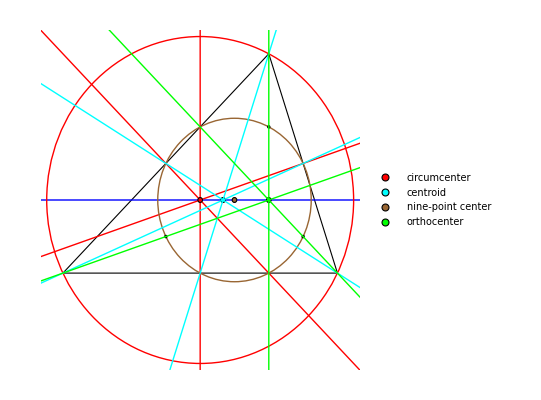

```mathematica
tri={{-14,-6},{10,-6},{4,12}};
euler= EulerLinePoints[tri];
mids=Mean/@Subsets[Reverse[tri],{2}];
otherthree=Mean[{#,euler[[4]]}]&/@tri;
Legended[Graphics[{EdgeForm[Black],White,Thick,Triangle[tri],
Blue, InfiniteLine[Take[euler,2]],Thin,
Red, InfiniteLine[{euler[[1]],#}]&/@mids,Circumsphere[tri],Disk[euler[[1]],0.2],
Cyan,InfiniteLine/@Transpose[{tri,mids}],Disk[euler[[2]],0.2],
Brown,Circle[euler[[3]],EuclideanDistance[euler[[3]],mids[[1]]]],Disk[#,.1]&/@otherthree,Disk[euler[[3]],0.2],
Green, InfiniteLine[{euler[[4]],#}]&/@tri,Disk[euler[[4]],0.2]}],PointLegend[{Red,Cyan,Brown,Green},{"circumcenter","centroid","nine-point center","orthocenter"},LegendMarkers->ConstantArray[Graphics[Disk[]],3]]]
```

## Source & Additional Information

### Contributed By

Ed Pegg Jr

### Keywords

Euler line

circumcenter

centroid

nine point center

orthocenter

perpendicular bisectors

medians

altitudes

triangle

### Categories

Geometry

Visualization & Graphics

### Related Symbols

Triangle

TriangleConstruct

### Related Resource Objects

GergonnePoint

Monge

NagelPoint

Orthocenter

### Source/Reference Citation

Source, reference or citation information

### Links

Euler Line

Orthocenter

Nine-Point Circle

Triangle Calculator

Tetrahedron Centers

### Tests

```mathematica
VerificationTest[EulerLinePoints/@{{{-2,-6},{-2,6},{4,0}},{{-6,-6},{-6,6},{12,0}},{{-10,14},{-4,-16},{14,2}},{{-10,6},{-4,-12},{14,6}},{{-10,-6},{-4,12},{14,-6}},{{-10,-14},{-4,16},{14,-2}},{{-12,-24},{-12,24},{24,0}},{{-16,-24},{-16,24},{32,0}},{{1,2},{3,4},{0,0}}},{{{-2,0},{0,0},{1,0},{4,0}},{{2,0},{0,0},{-1,0},{-4,0}},{{-2,0},{0,0},{1,0},{4,0}},{{2,0},{0,0},{-1,0},{-4,0}},{{2,0},{0,0},{-1,0},{-4,0}},{{-2,0},{0,0},{1,0},{4,0}},{{-2,0},{0,0},{1,0},{4,0}},{{2,0},{0,0},{-1,0},{-4,0}},{{15/2,-5/2},{4/3,2},{-7/4,17/4},{-11,11}}}]
```

TestResultObject[…]

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.